## Seminarska naloga pri ROM-u Nihanje, valovanje in optika Matura 2017 - jesenski rok

## Otroška gugalnica je zgrajena iz dveh lahkih vrvic, na katerih je pritrjen sedež. Otrok, ki sedi na gugalnici, ima skupaj s sedežem z maso 40 kg . Vrvici sta dolgi 3,0 m in sta pripeti na vejo drevesa tako, da je sedež v ravnovesni legi 50 cm nad tlemi. Privzemite, da je težišče sistema na višini sedeža. Otrok se začne poganjati in pri prvih desetih nihajih se energija nihanja poveča za 16 J pri vsakem nihaju. Po desetih nihajih se otrok poganja le še toliko, da vzdržuje stalno amplitudo nihanja. Ta je dovolj majhna, da lahko gugalnico pri vseh vprašanjih te naloge obravnavamo kot sinusno.

## -Graphics-

# Osnovne enote za računanje in podatki:

Težni pospešek :

```mathematica
g := 9.8
```

Masa otroka in gugalnice:

```mathematica
m := 40
```

Začetna  energija nihanja:

```mathematica
Subscript[W, zac]:=  16
```

Dolžina vrvice:

```mathematica
l := 3
```

Število nihajev:

```mathematica
Subscript[N, i]:= 10
```

Radiani v stopinje:

```mathematica
Rad := 180 / π
```

# 1. Izračunajte nihajni čas in frekvenco nihanja gugalnice.

```mathematica
Subscript[t, 0] = 2 * π * Sqrt[l / g]
```

3.47638

```mathematica
V = N[1 / Subscript[t, 0]]
```

0.287655

# 2. Izračunajte hitrost, s katero se po desetih nihajih otrok giblje skozi ravnovesno lego.

```mathematica
Subscript[W, k0] = Subscript[N, i] * Subscript[W, zac]
```

160

```mathematica
Subscript[v, 0] = N[Sqrt[2* Subscript[W, k0]/ m]]
```

2.82843

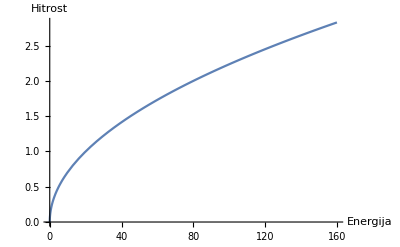

```mathematica
Plot[Sqrt[2* Subscript[W, k0]/ m],{Subscript[W, k0],0, 160}, AxesLabel-> {Energija, Hitrost}]
```

# 3. Izračunajte, koliko časa po tem, ko se je otrok gibal skozi ravnovesno lego, je pospešek nihanja prvič enak polovici največjega pospeška.

```mathematica
t = Subscript[t, 0] / (2 * π) * Sin[1 / 2]
```

0.265534

# 4. Izračunajte amplitudo odmika gugalnice od ravnovesne lege po desetih nihajih.

```mathematica
Subscript[x, 0]= Subscript[t, 0]/ (2 * π)* Sqrt[(2 * Subscript[W, k0])/ m]
```

1.56492

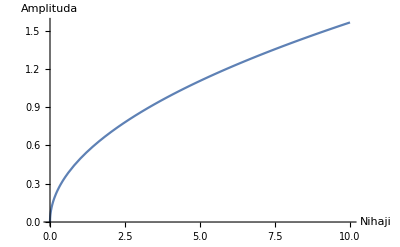

```mathematica
Plot[Subscript[t, 0]/ (2 * π)* Sqrt[(2 * Subscript[N, i] * Subscript[W, zac])/ m],{Subscript[N, i],0, 10}, AxesLabel-> {Nihaji, Amplituda}]
```

# 5. Izračunajte kot, ki ga po desetih nihajih v skrajni legi vrvici gugalnice oklepata z navpičnico.

```mathematica
Subscript[ϕ, 0]= (Subscript[x, 0] / l) * Rad
```

29.8878

# 6. Narišite graf časovne odvisnosti potencialne energije otroka glede na ravnovesno lego v odvisnosti od časa za vsaj dva nihajna časa nihanja gugalnice. Kot začetni trenutek na grafu izberite prehod gugalnice skozi ravnovesno lego.

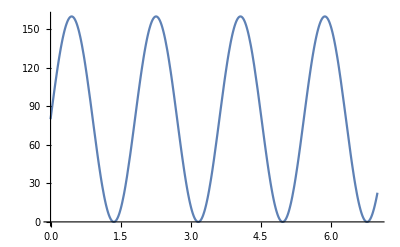

```mathematica
Plot[(Sin[Subscript[x, 0] / V] + 1) * Subscript[W, k0]/ 2,{Subscript[x, 0],0, 7}, AxesLabel-> {Čas, Energija}]
```

# Čez nekaj časa se otrok povsem neha poganjati, zato se gugalnici pri vsakem naslednjem nihaju energija nihanja zmanjša za 15 % . 7. Izračunajte, čez koliko časa po koncu poganjanja gugalnice je amplituda nihanja polovico tiste, s katero je nihala gugalnica po desetih nihajih od začetka nihanja.

```mathematica
Subscript[W, nih] := 1/2*m *((2 * π) / Subscript[t, 0]) ^2 * Subscript[x, 0]^2
Subscript[x, 1] := Sqrt[Subscript[W, nih1]/ Subscript[W, nih]] * Subscript[x, 0]
Subscript[W, nih1] := Subscript[W, nih] / 4
```

```mathematica
t = DecimalForm[Subscript[t, 0] * Log[0.25] / Log[0.85]]
```

29.6537